```mathematica
SetOptions[Plot,BaseStyle->FontSize->20];
SetOptions[ContourPlot,BaseStyle->{FontSize->20, FontColor ->  Black}];
```

```mathematica
hbar=1.05457148×10(10)^-34; Delta = 9.2 10^12;Gam = 32.8 10^6/(2 Pi);λ = 852.1 10^-9; Inti = 2000000;Ints = 3;mCs = (133 1.660 10^-27);Er = hbar^2 k^2/(2*mCs);
alal = 2;k= 2 Pi/λ;
el = 1.602 10^-19;
me = 9.1 10^-31;
```

```mathematica
Clear[a,b,x,y,z, hbar, Gam, Inti, Ints, Delta,k]
```

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

```mathematica
ϵ1 = {r Exp[-ⅈ*k*z], Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z]+ ⅈ r Exp[-ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y] }
ϵ1s = {r Exp[+ⅈ*k*z], Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z]- ⅈ r Exp[+ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}
```

{(1.+0. ⅈ) r,(1.+0. ⅈ)+(ⅇ^((0.-7.37377×10^6 ⅈ) x))/(√2)+(ⅇ^((0.+7.37377×10^6 ⅈ) x))/(√2)+(0.+1. ⅈ) r,(ⅇ^((0.-7.37377×10^6 ⅈ) x))/(√2)+(ⅇ^((0.+7.37377×10^6 ⅈ) x))/(√2)+ⅇ^((0.+7.37377×10^6 ⅈ) y)}

{(1.+0. ⅈ) r,(1.+0. ⅈ)+(ⅇ^((0.-7.37377×10^6 ⅈ) x))/(√2)+(ⅇ^((0.+7.37377×10^6 ⅈ) x))/(√2)-(0.+1. ⅈ) r,(ⅇ^((0.-7.37377×10^6 ⅈ) x))/(√2)+(ⅇ^((0.+7.37377×10^6 ⅈ) x))/(√2)+ⅇ^((0.-7.37377×10^6 ⅈ) y)}

```mathematica
ecrossold = +1/3*hbar Gam^2 Inti / (Delta*8 Ints)ⅈ*Cross[{0, Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]},{0, Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}]//FullSimplify
```

{1/(12 Delta Ints)Gam^2 hbar Inti (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}

```mathematica
ecrosssold = {1/(12 Delta Ints)Gam^2 hbar Inti (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}
```

{1.73542×10^-28 (-Sin[7.37377×10^6 (x-y)]/(√2)+Sin[7.37377×10^6 y]+Sin[7.37377×10^6 (x+y)]/(√2)),0,0}

```mathematica
+1/3*hbar Gam^2 Inti / (Delta*8 Ints)
```

```mathematica
ecross =  ⅈ*Cross[ϵ1,ϵ1s]//FullSimplify
```

{-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}

```mathematica
ecrosss[x_,y_,z_,a_,b_] := +1/3*hbar Gam^2 Inti / (Delta*8 Ints){-2 (r Cos[k (y+z)]+Sin[a-b] Sin[2 k x]+Sin[a] Sin[k (x-y)]-Sin[b] Sin[k (x+y)]+Cos[a] (r Cos[k (x+z)]-Sin[k (x-z)])-Sin[k (y-z)]+Cos[b] (r Cos[k (x-z)]+Sin[k (x+z)])),2 r (Cos[b] Sin[k (x-z)]-Cos[a] Sin[k (x+z)]-Sin[k (y+z)]),2 r (r+Cos[k z] (Sin[a]-Sin[b]) Sin[k x]+Cos[k x] (Sin[a]+Sin[b]) Sin[k z]+Sin[2 k z])}
```

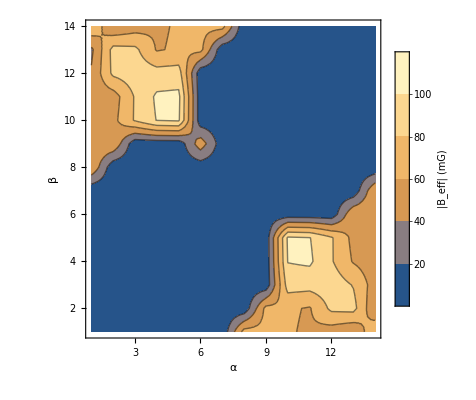
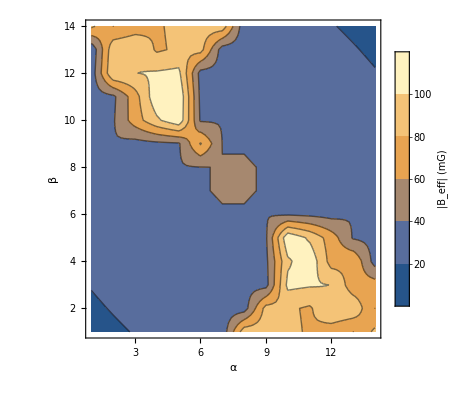
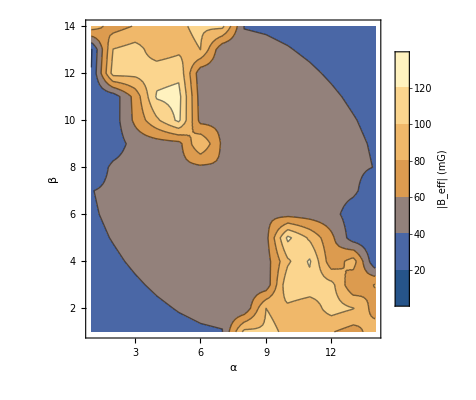
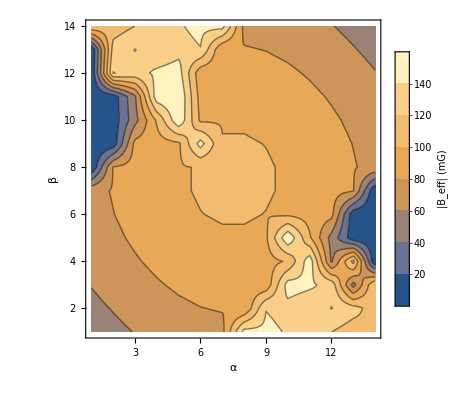
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1],

r=0.5;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1]},
{

r=0.7;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1],

r=1.2;
ListContourPlot[ Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}};Sqrt[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b].ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/13}],PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}], FrameLabel->{"α","β"}, FrameStyle -> Black,InterpolationOrder->1]


}}]
```

```mathematica
a= Pi/4; b = -Pi/4; r= 1
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}
Plot3D[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]/(0.7*el hbar/(2 me)) * 10^4*10^3,{a, -Pi/2, Pi/2},{b, -Pi/2, Pi/2},PlotLegends-> BarLegend[All,None,LegendMarkerSize->250, LegendLabel -> "|B_eff| (mG)", LabelStyle -> {FontSize -> 20}]]
```

1

{0,{x→-3.4084×10^-7,y→-4.2605×10^-7,zf→-2.5563×10^-7}}

-Graphics3D-

```mathematica
Direction of Beff
```

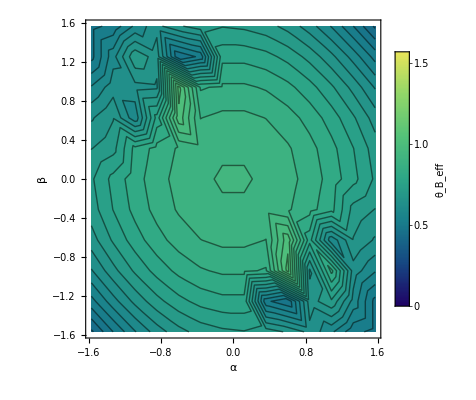

```mathematica
r=2.3;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/13},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, Pi/2}}], PlotRange->{ All, All, {0,Pi/2}}, Contours ->30, InterpolationOrder->5]
```

```mathematica
ToSphericalCoordinates[{0,-1,0}]
```

{1,π/2,-π/2}

```mathematica
ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]
```

1.34933

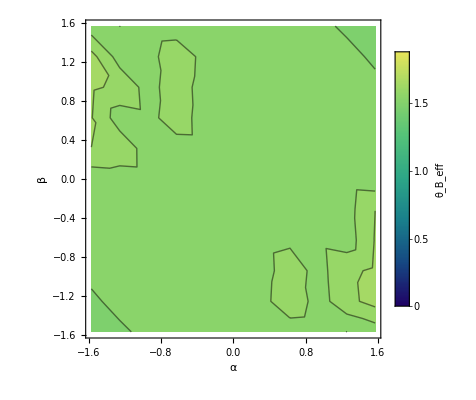
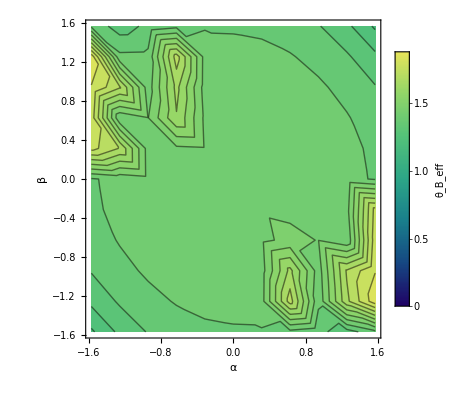
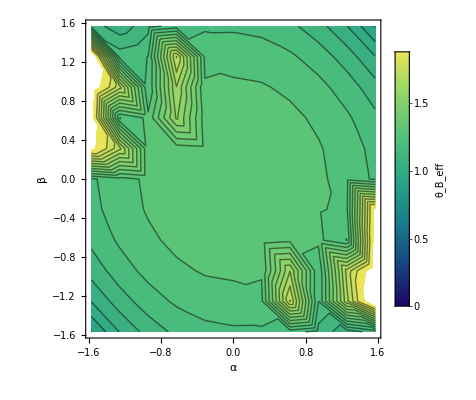
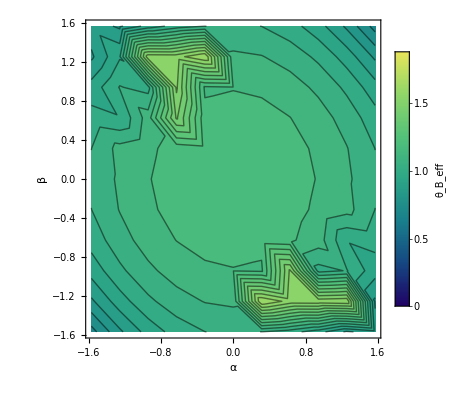
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
r=0.1;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
,

r=0.4;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
},
{

r=0.8;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]
,

r=1.2;
ListContourPlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/10},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {a,b , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{a, -Pi/2, Pi/2, Pi/10},{b, -Pi/2, Pi/2, Pi/10}],1], PlotLegends->BarLegend[{Automatic,{0,1.2Pi/2}},None, LegendLabel-> "θ_B_eff"], FrameLabel->{"α","β"},ColorFunctionScaling->False, FrameStyle -> Black,InterpolationOrder->2,ColorFunction-> ColorData[{"BlueGreenYellow",{0, 1.2Pi/2}}], PlotRange->{ All, All, {0,1.2Pi/2}}, Contours ->30, InterpolationOrder->5]


}}]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

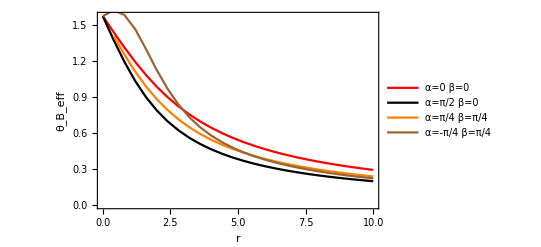

```mathematica
Show[{a= 0; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.4}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=0  β=0"}],Above]],
a= Pi/2; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.4}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Black, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=π/2  β=0"}],Above]],

a= Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.4}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Orange, FrameStyle-> Black, Frame-> True, PlotLegends->Placed[LineLegend[{"α=π/4  β=π/4"}],Above]],


a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[2]]},{r, 0,10, 0.4}],0], FrameLabel->{"r","θ_B_eff"},PlotStyle ->Brown, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=-π/4  β=π/4"}],Above]]
}]
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

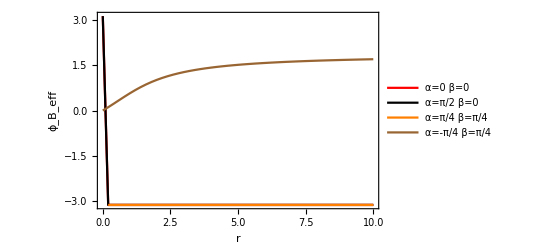

```mathematica
Show[{a= 0; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=0  β=0"}],Above]],
a= Pi/2; b= 0;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Black, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=π/2  β=0"}],Above]],

a= Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Orange, FrameStyle-> Black, Frame-> True, PlotLegends->Placed[LineLegend[{"α=π/4  β=π/4"}],Above]],


a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,10, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Brown, FrameStyle-> Black, Frame-> True,PlotLegends->Placed[LineLegend[{"α=-π/4  β=π/4"}],Above]]
}]
```

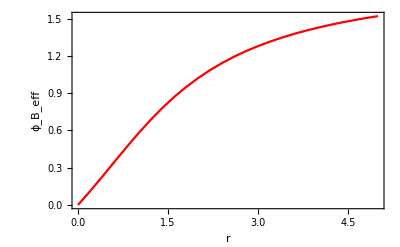

```mathematica
a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[3]]},{r, 0,5, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True]
```

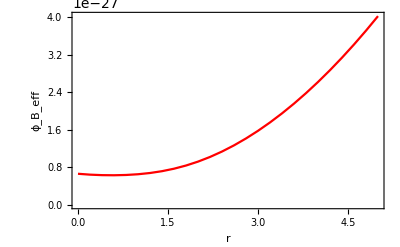

```mathematica
a= -Pi/4; b= Pi/4;
ListLinePlot[ Flatten[Table[
udsmintest = Flatten[Table[{{x,y,zf}, UDsim[x,y,zf,a,b]/Er},{x,-1λ/2,1* 1λ/2, λ/10},{y,-1λ/2,1λ/2,λ/13},{zf,- 1λ/2,1λ/2,λ/10}],2];
res = (Pick[#1,#2,Min[#2]]&@@Transpose[udsmintest])[[1]];
mi = {0, {x-> res[[1]], y -> res[[2]], zf -> res[[3]]}}; {r , ToSphericalCoordinates[ecrosss[x /. mi[[2]],y/. mi[[2]],zf/. mi[[2]],a,b]][[1]]},{r, 0,5, 0.2}],0], FrameLabel->{"r","ϕ_B_eff"},PlotStyle ->Red, FrameStyle-> Black, Frame-> True]
```